# Albañil volador

Ref: https://www.youtube.com/watch?v=F-4xVAghgfc

### Planteamiento del problema

```mathematica
L = 1/2(m1+m2)x1'[t]^2+1/2 m1 θ1'[t]^2 x1[t]^2+1/2 m2 θ2'[t]^2 x1[t]^2+1/2 l^2 m2 θ2'[t]^2-m2 θ2'[t]^2 l x1[t]+m1 g x1[t] Cos[θ1[t]]+m2 g (l-x1[t])Cos[θ2[t]];
```

Ec para x1(t)

```mathematica
D[D[L,x1'[t]],t]
```

(m1+m2) x1''[t]

```mathematica
D[L,x1[t]]
```

g m1 Cos[θ1[t]]-g m2 Cos[θ2[t]]+m1 x1[t] θ1'[t]^2-l m2 θ2'[t]^2+m2 x1[t] θ2'[t]^2

```mathematica
Solve[(m1+m2) x1''[t]==g m1 Cos[θ1[t]]-g m2 Cos[θ2[t]]+m1 x1[t] θ1'[t]^2-l m2 θ2'[t]^2+m2 x1[t] θ2'[t]^2,x1''[t]]
```

{{x1''[t]→(g m1 Cos[θ1[t]]-g m2 Cos[θ2[t]]+m1 x1[t] θ1'[t]^2-l m2 θ2'[t]^2+m2 x1[t] θ2'[t]^2)/(m1+m2)}}

Ec para θ1(t)

```mathematica
D[D[L,θ1'[t]],t]
```

2 m1 x1[t] x1'[t] θ1'[t]+m1 x1[t]^2 θ1''[t]

```mathematica
D[L,θ1[t]]
```

-g m1 Sin[θ1[t]] x1[t]

```mathematica
Solve[2 m1 x1[t] x1'[t] θ1'[t]+m1 x1[t]^2 θ1''[t]==-g m1 Sin[θ1[t]] x1[t],θ1''[t]]
```

{{θ1''[t]→(-g Sin[θ1[t]]-2 x1'[t] θ1'[t])/x1[t]}}

Ec para θ2(t)

```mathematica
D[D[L,θ2'[t]],t]
```

-2 l m2 x1'[t] θ2'[t]+2 m2 x1[t] x1'[t] θ2'[t]+l^2 m2 θ2''[t]-2 l m2 x1[t] θ2''[t]+m2 x1[t]^2 θ2''[t]

```mathematica
D[L,θ2[t]]
```

-g m2 Sin[θ2[t]] (l-x1[t])

```mathematica
Solve[-2 l m2 x1'[t] θ2'[t]+2 m2 x1[t] x1'[t] θ2'[t]+l^2 m2 θ2''[t]-2 l m2 x1[t] θ2''[t]+m2 x1[t]^2 θ2''[t]==-g m2 Sin[θ2[t]] (l-x1[t]),θ2''[t]]
```

{{θ2''[t]→(-g Sin[θ2[t]]+2 x1'[t] θ2'[t])/(l-x1[t])}}

### Solución numérica

```mathematica
h1 = 3*3;
h2 = 2;
hc = 4*3-h1;
hp = 5*3;
d1 = 1;
d2 = 1.5;
m1 = 70;
m2 = 50;
g = 9.8;
```

```mathematica
θ1Initial = -N[ArcTan[d1/(hp-h1)]]
```

-0.165149

```mathematica
θ2Initial = N[ArcTan[d1/(hp-h2)]]
```

0.0767719

```mathematica
x1Initial = N[√((hp-h1)^2+d1^2)]
```

6.08276

```mathematica
x2Initial = N[√((hp-h2)^2+d2^2)]
```

13.0863

```mathematica
l = x1Initial + x2Initial
```

19.169

```mathematica
solutions = NDSolveValue[
{
x1''[t]==(g m1 Cos[θ1[t]]-g m2 Cos[θ2[t]]+m1 x1[t] θ1'[t]^2-l m2 θ2'[t]^2+m2 x1[t] θ2'[t]^2)/(m1+m2),
θ1''[t]==(-g Sin[θ1[t]]-2 x1'[t] θ1'[t])/x1[t],
θ2''[t]==(-g Sin[θ2[t]]+2 x1'[t] θ2'[t])/(l-x1[t])
,
WhenEvent[x1[t] Cos[θ1[t]]==hp,tMax=t;"StopIntegration"]
,
x1[0]==x1Initial,x1'[0]==0,
θ1[0]==θ1Initial,θ1'[0]==0,
θ2[0]==θ2Initial,θ2'[0]==0
},
{x1[t],θ1[t],θ2[t]},
{t,0,10}
];
```

```mathematica
tMax
```

3.30253

```mathematica
solutions
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
r1[x1_,θ1_,θ2_]:={x1 Sin[θ1],-x1 Cos[θ1]};
r2[x1_,θ1_,θ2_]:={(l-x1) Sin[θ2],-(l-x1) Cos[θ2]};
r1[tP_]:=Apply[r1,solutions/.t->tP];
r2[tP_]:=Apply[r2,solutions/.t->tP];
```

```mathematica
Manipulate[ParametricPlot[{r1[t],r2[t]},{t,0,tp},PlotLegends->"Expressions"],{{tp,tMax},0.01,tMax},SaveDefinitions->True]
```

```mathematica
Diagram[r1_,r2_]:=Graphics[
{
Line[{{0,0},r1}],
Line[{{0,0},r2}],
Yellow,Disk[{0,0},0.1],
Green,Disk[r1,0.1],
Red,Disk[r2,0.1],
Blue,Disk[{x1Initial Sin[θ1Initial],-x1Initial Cos[θ1Initial]}+{0,hc},0.1],
Brown,Line[{{-2,-hp},{2,-hp}}]
},
ImageSize->150,
PlotRange->{{-2,2},{-16,1}}
];
```

```mathematica
Manipulate[
Show[
Diagram[r1[t],r2[t]],
ParametricPlot[{r1[tp],r2[tp]},{tp,0,t}]
],
{t,0.0001,tMax}
]
```

### Gráfica de la solución

```mathematica
PlotSolution[h2_,d1_,d2_,m1_,m2_]:=DynamicModule[{θ1Initial,θ2Initial,x1Initial,x2Initial,l,solutions,tMax,r1,r2},
θ1Initial = -N[ArcTan[d1/(hp-h1)]];
θ2Initial = N[ArcTan[d2/(hp-h2)]];
x1Initial = N[√((hp-h1)^2+d1^2)];
x2Initial = N[√((hp-h2)^2+d2^2)];
l = x1Initial + x2Initial;
solutions = NDSolveValue[
{
x1''[t]==1/(m1+m2)(g m1 Cos[θ1[t]]-g m2 Cos[θ2[t]]+m1 x1[t] θ1'[t]^2-l m2 θ2'[t]^2+m2 x1[t] θ2'[t]^2),
θ1''[t]==(-g Sin[θ1[t]]-2 x1'[t] θ1'[t])/x1[t],
θ2''[t]==(-g Sin[θ2[t]]+2 x1'[t] θ2'[t])/(l-x1[t])
,
WhenEvent[x1[t] Cos[θ1[t]]==hp,tMax=t;"StopIntegration"]
,
x1[0]==x1Initial,x1'[0]==0,
θ1[0]==θ1Initial,θ1'[0]==0,
θ2[0]==θ2Initial,θ2'[0]==0
},
{x1[t],θ1[t],θ2[t]},
{t,0,10}
];

r1[x1_,θ1_,θ2_]:={x1 Sin[θ1],-x1 Cos[θ1]};
r2[x1_,θ1_,θ2_]:={(l-x1) Sin[θ2],-(l-x1) Cos[θ2]};
r1[tP_]:=Apply[r1,solutions/.t->tP];
r2[tP_]:=Apply[r2,solutions/.t->tP];

Manipulate[
Show[
Diagram[r1[t],r2[t]],
ParametricPlot[{r1[tp],r2[tp]},{tp,0,t}]
],
{{t,tMax},0.0001,tMax},
SaveDefinitions->True
]
];
```

```mathematica
PlotSolution[h2,d1,d2,m1,m2]
```

### Posición final de la masa 2

```mathematica
DistanceToCompa[h2_,d1_,d2_,m1_,m2_]:=Block[{θ1Initial,θ2Initial,x1Initial,x2Initial,l,solutions,tMax,r1,r2,compaPosition},
θ1Initial = -N[ArcTan[d1/(hp-h1)]];
θ2Initial = N[ArcTan[d2/(hp-h2)]];
x1Initial = N[√((hp-h1)^2+d1^2)];
x2Initial = N[√((hp-h2)^2+d2^2)];
l = x1Initial + x2Initial;
compaPosition = {x1Initial Sin[θ1Initial],-x1Initial Cos[θ1Initial]}+{0,hc};

solutions = NDSolveValue[
{
x1''[t]==1/(m1+m2)(g m1 Cos[θ1[t]]-g m2 Cos[θ2[t]]+m1 x1[t] θ1'[t]^2-l m2 θ2'[t]^2+m2 x1[t] θ2'[t]^2),
θ1''[t]==(-g Sin[θ1[t]]-2 x1'[t] θ1'[t])/x1[t],
θ2''[t]==(-g Sin[θ2[t]]+2 x1'[t] θ2'[t])/(l-x1[t])
,
WhenEvent[x1[t] Cos[θ1[t]]==hp,tMax=t;"StopIntegration"]
,
x1[0]==x1Initial,x1'[0]==0,
θ1[0]==θ1Initial,θ1'[0]==0,
θ2[0]==θ2Initial,θ2'[0]==0
},
{x1[t],θ1[t],θ2[t]},
{t,0,10}
];

r1[x1_,θ1_,θ2_]:={x1 Sin[θ1],-x1 Cos[θ1]};
r2[x1_,θ1_,θ2_]:={(l-x1) Sin[θ2],-(l-x1) Cos[θ2]};
r1[tP_]:=Apply[r1,solutions/.t->tP];
r2[tP_]:=Apply[r2,solutions/.t->tP];

Norm[r2[tMax]-compaPosition]
];
```

```mathematica
DistanceToCompa[h2,d1,d2,m1,m2]
```

0.980936

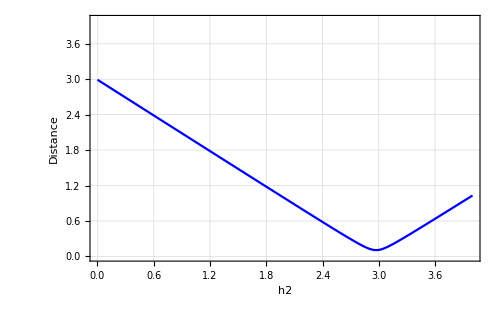

```mathematica
Plot[
DistanceToCompa[h2,d1,d2,m1,m2],{h2,0,4},
PlotRange->{All,{0,4}},
PlotTheme->"Monochrome",
FrameLabel->{Style["h2",15], Style["Distance",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Frame->True,
ImageSize->500,
PlotStyle->Blue
]
```

```mathematica
Plot3D[
{DistanceToCompa[h2,d1,d2,m1,m2],0},{h2,0,4},{d2,0,3},
AxesLabel->{Style["h2",15], Style["d2",15],Style["Distance",15]}
]
```

-Graphics3D-

```mathematica
distByParams = Table[{h2,d2,DistanceToCompa[h2,d1,d2,m1,m2]},{h2,0,4,0.05},{d2,0,3,0.05}];
```

```mathematica
ListPointPlot3D[Flatten[distByParams,1]]
```

-Graphics3D-

```mathematica
MinimalBy[Flatten[distByParams,1],Last]
```

{{3.,1.7,0.0157605}}

```mathematica
PlotSolution[3,d1,1.7,m1,m2]
```